```mathematica
Clear["Global`*"];
J={{0,1,-1},{1,0,1},{-1,1,0}};
H0[z_]:=DiagonalMatrix[{-1+3z,-1+z,1+z,-1-z,-1+z,1-z,-1-z,-1-3z}];
V=-{{0,1,1,0,1,0,0,0},{1,0,0,1,0,1,0,0},{1,0,0,1,0,0,1,0},{0,1,1,0,0,0,0,1},{1,0,0,0,0,1,1,0},{0,1,0,0,1,0,0,1},{0,0,1,0,1,0,0,1},{0,0,0,1,0,1,1,0}};
H[z_,hx_]:=H0[z]+hx*V;
Hnew[hx_]:=Drop[Drop[Transpose[Drop[Drop[H[0,hx],{3}],{5}]],{3}],{5}];
H2[J_,hx_]:=-hx^2/2/J*{{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1}};
H3Term[hx_] :=hx^3*0.5*{{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0}};
H3[J_,hx_]:=Hnew[hx]+H2[J,hx];
```

Calculate and plot approximated GS energy

```mathematica
energynew={};
energyArraynew={};
hx=Range[0,0.1,0.001];
Do[energynew=Append[energynew,Sort[N[Eigenvalues[H3[1,hx[[i]]]]],Less]],{i,Length[hx]}];
Do[AppendTo[energyArraynew,Table[{hx[[i]],energynew[[i]][[k]]},{i,1,Length[hx]}]],{k,1,Length[energynew[[1]]]}]
P1=ListPlot[energyArraynew]
```

-Graphics-

Calculate and plot exact GS energies

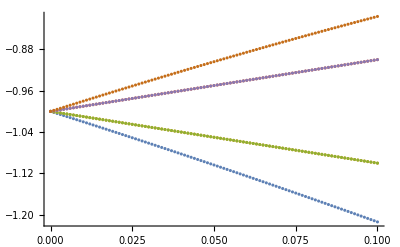

```mathematica
energy={};
energyArray={};
Do[energy=Append[energy,Sort[N[Eigenvalues[H[0,hx[[i]]]]],Less]],{i,Length[hx]}];
Do[AppendTo[energyArray,Table[{hx[[i]],energy[[i]][[k]]},{i,1,Length[hx]}]],{k,1,Length[energy[[1]]]}]
GSenergyArray=Drop[energyArray,-2];
P2=ListPlot[GSenergyArray]
```

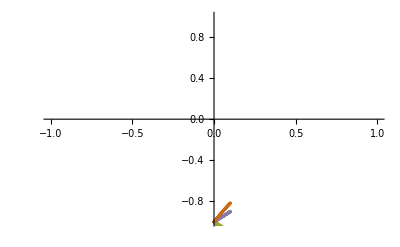

```mathematica
Show[P1,P2]
```

Calculate and plot energy errors

```mathematica
errorRow={};
errorArray={};
Do[
AppendTo[errorArray,Table[{hx[[j]],Abs[energyArraynew[[i]][[j]][[2]]-GSenergyArray[[i]][[j]][[2]]]},{j,Length[hx]}]],
{i,Length[energyArraynew]}]
cubicfit=Fit[errorArray[[1]],{1,x^3},x];
ListPlot[errorArray,PlotLegends->Automatic,PlotRange->All]
ListLogLogPlot[errorArray[[1]],PlotLegends->Automatic,PlotRange->All]
Show[ListPlot[errorArray[[1]],PlotLegends->Automatic,PlotRange->All],Plot[cubicfit,{x,0,1}]]
```

-Graphics-

-Graphics-

-Graphics-

Compare 6 probabilities; difference between exact probabilities and the approximate probabilities

Plot exact probability

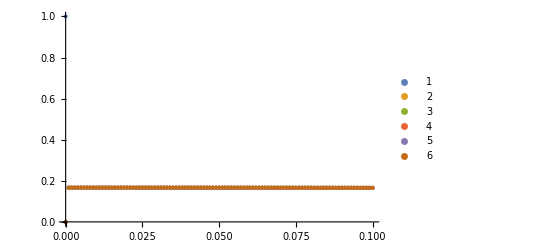

```mathematica
data1={};
Do[
eigensystem=Eigensystem[H[0,hx[[x]]]];
eigenvalues=eigensystem[[1,;;]];
GSIndex=Ordering[N[eigenvalues],1];
eigenvectors=eigensystem[[2,;;]];
GSEigenvector=eigenvectors[[GSIndex]];
norm=(GSEigenvector.ConjugateTranspose[GSEigenvector])[[1]][[1]];NormedGSEigenvector=Transpose[GSEigenvector]/√norm;GSProbability=Conjugate[NormedGSEigenvector]*NormedGSEigenvector;
data1=Append[data1,N[GSProbability]],
{x,Length[hx]}];
tableArray1={};
Do[AppendTo[tableArray1,Table[{hx[[i]],data1[[i]][[k]][[1]]},{i,Length[hx]}]],{k,1,Length[data1[[1]]]}]
ExactProbabilityArray=Drop[Drop[tableArray1,{3}],{5}];
P3=ListPlot[ExactProbabilityArray,PlotLegends->Automatic,PlotRange->All]
```

Plot approximate probability

```mathematica
data2={};
Do[
eigensystem=Eigensystem[H3[1,hx[[x]]]];
eigenvalues=eigensystem[[1,;;]];
GSIndex=Ordering[N[eigenvalues],1];
eigenvectors=eigensystem[[2,;;]];
GSEigenvector=eigenvectors[[GSIndex]];
norm=(GSEigenvector.ConjugateTranspose[GSEigenvector])[[1]][[1]];NormedGSEigenvector=Transpose[GSEigenvector]/√norm;GSProbability=Conjugate[NormedGSEigenvector]*NormedGSEigenvector;
data2=Append[data2,N[GSProbability]],
{x,Length[hx]}];
tableArray2={};
Do[AppendTo[tableArray2,Table[{hx[[i]],data2[[i]][[k]][[1]]},{i,Length[hx]}]],{k,1,Length[data2[[1]]]}]
P4=ListPlot[tableArray2,PlotLegends->Automatic,PlotRange->All]
```

$Aborted

Part::partw: Part 3 of {{{Divide[25. <<9>>[<<1>>] <<1>> (-0.2 + 1. H3[0.] - 0.2 Root[1.000000000000000 + <<7>> & , 1]), <<1>>]}, <<5>>}, {<<6>>}} does not exist.

Part::partw: Part 4 of {{{Divide[25. <<9>>[<<1>>] <<1>> (-0.2 + 1. H3[0.] - 0.2 Root[1.000000000000000 + <<7>> & , 1]), <<1>>]}, <<5>>}, {<<6>>}} does not exist.

Part::partw: Part 5 of {{{Divide[25. <<9>>[<<1>>] <<1>> (-0.2 + 1. H3[0.] - 0.2 Root[1.000000000000000 + <<7>> & , 1]), <<1>>]}, <<5>>}, {<<6>>}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification 3⟦1⟧ is longer than depth of object.

Part::partd: Part specification 4⟦1⟧ is longer than depth of object.

Part::partd: Part specification 5⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Compare graphs

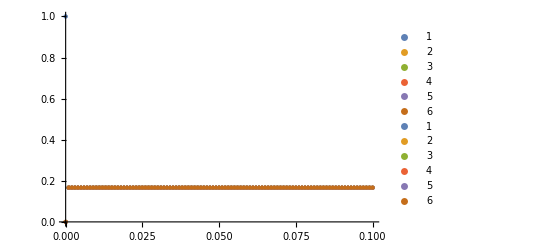

```mathematica
Show[P3,P4]
```

Calculate and plot probability errors

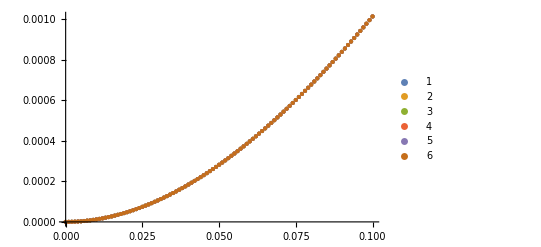

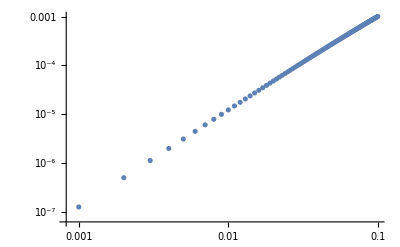

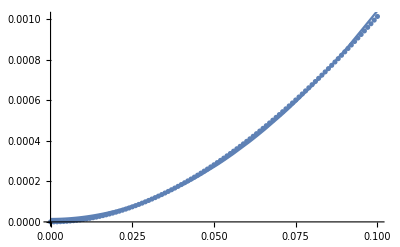

```mathematica
ProbabilityErrorArray={};
Do[
AppendTo[ProbabilityErrorArray,Table[{hx[[j]],Abs[tableArray2[[i]][[j]][[2]]-ExactProbabilityArray[[i]][[j]][[2]]]},{j,Length[hx]}]],
{i,Length[tableArray2]}]
quadraticfit=Fit[ProbabilityErrorArray[[1]],{1,x^2},x];
ListPlot[ProbabilityErrorArray,PlotLegends->Automatic,PlotRange->All]
ListLogLogPlot[ProbabilityErrorArray[[1]],PlotLegends->Automatic,PlotRange->All]
Show[ListPlot[ProbabilityErrorArray[[1]],PlotLegends->Automatic,PlotRange->All],Plot[quadraticfit,{x,0,1}]]
```